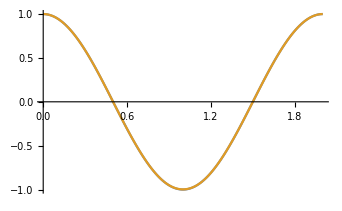

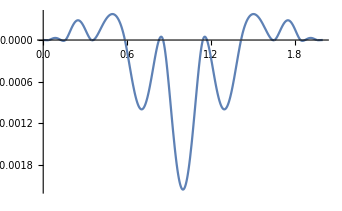

```mathematica
n = 11;
(* дефинираме функцията, която ще се интерполира *)
f[t_] := Cos[π*t];
(* интерполационните възли са: *)
Do[x[k] = 2*(Sin[(k*π)/(2*n)]^2), {k, 0, n}];
(* разстоянието между всеки два съседни възела -> Δ[k] *)
Do[Δ[k] = x[k+1] - x[k], {k, 0, n-1}];
(* методът на прогонката *)
(* 1. Изчисляваме коефициентите пред неизвестните s0, s1,..., sn *)
Do[cA[k] = 1/Δ[k-1], {k, 2, n-1}];
Do[cB[k] = 2/Δ[k-1] + 2/Δ[k], {k, 1, n - 1}];
Do[cC[k] = 1/Δ[k] , {k, 1, n - 2}];
(* Резултатът от дясната страна на равенството *)
Do[RightSide[k] = 3*(((f[x[k]] - f[x[k - 1]])/(Δ[k-1])^2) + ((f[x[k+1]] - f[x[k]]) /( Δ[k]^2))), {k, 1, n - 1}];
(* 2. Намираме α и β *)
α[1] = -cC[1]/cB[1];
β[1] = RightSide[1]/cB[1];
(* и изразяваме α[k] и β[k] *)
Do[α[k] = -cC[k]/(cA[k]*α[k-1] + cB[k]), {k, 2, n-2}];
Do[β[k] = (RightSide[k] - cA[k]*β[k-1])/(cA[k]*α[k-1] + cB[k]), {k, 2, n-1}]; 
(* намираме s[0] и s[n] *)
s[0] = f'[x[0]];
s[n]=f'[x[n]];
(*s[n-1] = beta[n-1];  ??? *)
Do[s[k] = α[k]*s[k+1] + β[k], {k, n - 1, 1, -1}];
(* общ вид на полиномите интерполиращи f(t) във всеки интервал на [0, 2], определен
от два последователни възела *)
Do[a[k]=(f[x[k+1]]-f[x[k]])/Δ[k]^2-s[k]/Δ[k],{k,0,n-1}];
Do[b[k] = s[k+1]/Δ[k]^2+s[k]/Δ[k]^2+2*(f[x[k]]-f[x[k+1]])/Δ[k]^3,{k,0,n-1}];
Do [polinom [k,t_] = f[x[k]] + s[k]*(t - x[k]) + a[k] (t - x[k])^2 + b[k]*(t - x[k])^2*(t - x[k+1]), {k, 0, n-1}];
(* построяваме кубичния сплайн за f(t) *)
Spline[t_]:=Sum[If[t≥x[k]&&t≤x[k+1], polinom[k, t], 0], {k, 0, n-1}];
(* графиките на функцията и сплайн функцията *)
Plot[{f[t],Spline[t]},{t,0,2},PlotPoints->300]

Plot[f[t]-Spline[t],{t,0,2},PlotRange->All]
```